```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 328 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
(m v^2)/r /. v-> r ω  /. r -> x
```

m x ω^2

```mathematica
-D[U[x], x] == (m v^2)/r /. v-> r ω  /. r -> x
```

-U'[x]==m x ω^2

```mathematica
Flatten[DSolve[ { -D[U[x], x] == (m v^2)/r /. v-> r ω  /. r -> x  , U[0] == 0 } , U[x] , x]]
```

{U[x]→-1/2 m x^2 ω^2}

```mathematica
DSolve[ { -D[U[x], x] == (m v^2)/r /. v-> r ω  /. r -> x  , U[0] == 0 } , U[x] , x][[1,1,2]]
DSolve[ { -D[U[x], x] == (m v^2)/r /. v-> r ω  /. r -> x  , U[0] == 0 } , U[x] , x][[1,1,2]] /. x-> b Sin[θ[t]]
```

-1/2 m x^2 ω^2

-1/2 b^2 m ω^2 Sin[θ[t]]^2

```mathematica
Clear[U]
U = 
DSolve[ { -D[U[x], x] == (m v^2)/r /. v-> r ω  /. r -> x  , U[0] == 0 } , U[x] , x][[1,1,2]] /. x-> b Sin[θ[t]]
```

-1/2 b^2 m ω^2 Sin[θ[t]]^2

```mathematica
Clear[s]
s = { b Sin[θ[t]] , b Cos[θ[t]]  }
```

{b Sin[θ[t]],b Cos[θ[t]]}

```mathematica
D[s, t]
```

{b Cos[θ[t]] θ'[t],-b Sin[θ[t]] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

b^2 Cos[θ[t]]^2 θ'[t]^2+b^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

b^2 Cos[θ[t]]^2 θ'[t]^2+b^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand  // Simplify
```

b^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand  // Simplify  )
```

1/2 b^2 m θ'[t]^2

```mathematica
Clear[V]
V = m g b Cos[θ[t]]
```

b g m Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - U - V   // Simplify 
ℒ // pdConv
```

1/2 b m (-2 g Cos[θ[t]]+b ω^2 Sin[θ[t]]^2+b θ'[t]^2)

1/2 b m (b ω^2 sin^2(θ(t))+b ((∂θ(t))/(∂t))^2-2 g cos(θ(t)))

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
D[ D[ ℒ , D[q, t] ], t ]  - D[ ℒ , q ] == 0 // Simplify
```

b m ((g+b ω^2 Cos[θ[t]]) Sin[θ[t]]-b θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

b m ((g+b ω^2 Cos[θ[t]]) Sin[θ[t]]-b θ''[t])==0

```mathematica
Clear[parameters]
parameters = {
b ->  2,
g-> 9.8 , 
ω-> 2 
} ; 
parameters // TableForm
```

b→2
g→9.8
ω→2

```mathematica
eqs /. parameters
```

2 m ((9.8+8 Cos[θ[t]]) Sin[θ[t]]-2 θ''[t])==0

```mathematica
Clear[ics]
ics = { 
θ[0] == π + 0.1 ,
θ'[0] == 0 
} ;
ics // TableForm
```

θ[0]==3.24159
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[{ eqs }/. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

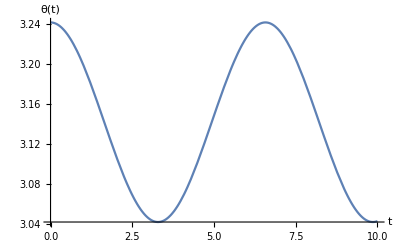

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 10 } , AxesLabel-> { t , q }  ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ[t]→InterpolatingFunction[…][t]}

θ[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q , D[q, t] } ]  ,
{ tmax , 1 , 50 } ]
```